```mathematica
thetaplus={};
thetaminus={};
lightlike={};
For[ttil=-Pi/1,ttil<=Pi/1,ttil+=0.01,
ll=Pi/2-Abs[ttil];
tplus=Pi/2;
tmin=-Pi/2;
AppendTo[thetaplus,{tplus,ttil}];
AppendTo[thetaminus,{tmin,ttil}];
AppendTo[lightlike,{ll,ttil}];
]
```

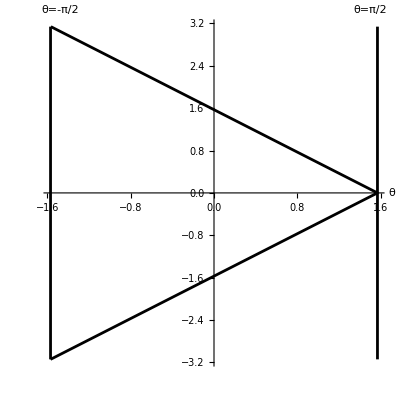

```mathematica
ListLinePlot[{thetaminus,thetaplus,lightlike},PlotStyle->Black,AspectRatio->1,Ticks->None, AxesLabel->{"θ",""},PlotLabels->Placed[{"θ=-π/2","θ=π/2",None},{Bottom,Bottom}]]
```